### Facts, so far

```mathematica
country[c_]:=Module[{countryMap=<|"Korea, South"->"South Korea"|>,q},q=countryMap[c];If[MissingQ[q],c,q]];
meta[c_]:=Module[{
totalMap=<|"US"->{"7 apr 2020",400000},"Italy"->{"7 apr 2020",155000},"Germany"->{"7 apr 2020",100000},"United Kingdom"->{"7 apr 2020",45000}|>,
growthMap=<|"US"->{"29 mar 2020",20000},"Italy"->{"13 mar 2020",7000},"Germany"->{"2 apr 2020",9000},"United Kingdom"->{"2 apr 2020",1500}|>,
accMap=<||>,
q,m},
m={"country"->CountryData[country[c],"Flag"]};
q=totalMap[c];If[!MissingQ[q],AppendTo[m,"total"->q]];
q=growthMap[c];If[!MissingQ[q],AppendTo[m,"growth"->q]];
q=accMap[c];If[!MissingQ[q],AppendTo[m,"acc"->q]];
m];
label[c_,t_]:=If[MemberQ[c["Properties"],t],Inset[Show[c["country"],ImageSize->30],c[t]],Nothing];
$exportDir="/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/";
```

```mathematica
world=Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
worldd=(row↦AssociationThread[Append[world[[1,;;4]],"data"],Append[row[[;;4]],TimeSeries[Transpose[{DateObject[{#,{"Month","/","Day","/","YearShort"}}]&/@world[[1,5;;]],row[[5;;]]}],MetaInformation->meta[row[[2]]]]]])/@Rest[world]//Dataset;
```

```mathematica
cc={"US","Italy","Germany","United Kingdom"};
```

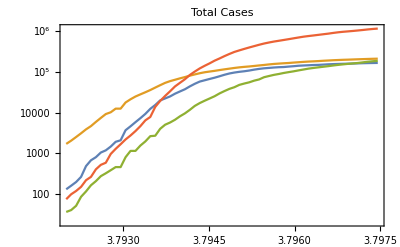

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/level.gif

```mathematica
worldd[Select[MemberQ[cc,#["Country/Region"]]∧#["Province/State"]==""&],TimeSeriesWindow[#data,{DateObject["1 mar 2020"],Automatic}]&][c↦Export[$exportDir<>"level.gif",DateListLogPlot[c,PlotLegends->((Show[#["country"],ImageSize->40](*//Framed*))&/@c),PlotLabel->"Total Cases",PlotRange->All,
Epilog->(label[#,"total"]&/@c)]//Echo]]
```

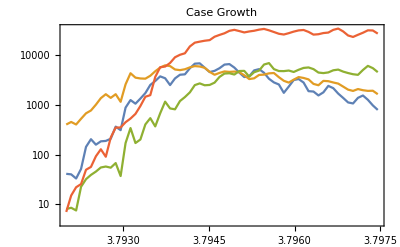

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/growth.gif

```mathematica
worldd[Select[MemberQ[cc,#["Country/Region"]]∧#["Province/State"]==""&],TimeSeriesWindow[Differences[#data,1,2]/2,{DateObject["1 mar 2020"],Automatic}]&][c↦Export[$exportDir<>"growth.gif",DateListLogPlot[c,PlotLegends->((Show[#["country"],ImageSize->40](*//Framed*))&/@c),PlotLabel->"Case Growth",PlotRange->All,Epilog->(label[#,"growth"]&/@c)]//Echo]]
```

### Swirl

```mathematica
pp=<|
"Brazil"-><|"ee"->5,"a"->10,"exp"->8,"y"->.000005|>,
"Denmark"-><|"ee"->4,"exp"->8,"y"->.000005,"a"->1|>,
"France"-><|"ee"->5,"exp"->8,"a"->1,"y"->-.00001|>,
"Germany"-><|"ee"->4,"exp"->1,"x"->-.000,"y"->.0000|>,
"India"-><|"a"->2,"x"->.000,"y"->.0000|>,
"Israel"-><|"ee"->3,"exp"->2,"a"->1,"y"->.000005|>,
"Italy"-><|"ee"->4,"a"->1,"exp"->2,"y"->-0.000005|>,
"Japan"-><|"ee"->3,"exp"->8,"a"->2,"y"->.00001|>,
"Poland"-><|"ee"->4,"exp"->4,"a"->5,"y"->-.000005|>,
"Russia"-><|"a"->2,"y"->-.000|>,
"Singapore"-><|"ee"->3,"exp"->2,"a"->1,"y"->.000015|>,
"South Africa"-><|"ee"->2,"exp"->2,"a"->5|>,
"Spain"-><|"ee"->4,"exp"->5|>,
"Sweden"-><|"a"->1,"ee"->3,"exp"->5,"y"->-.000005|>,
"Turkey"-><|"y"->-.000003|>,
"United Kingdom"-><|"ee"->4,"exp"->2,"a"->1,"y"->.0000|>,
"US"-><|"ee"->5,"exp"->2,"a"->1,"y"->.00|>
|>;
est2[r_,past_:0]:=Module[{iv,ig,mv,sol,ff,ff1,ee=5,Tmax,exp=2, a=1,ppc,mvPast,res},
Echo[r["c"]];
If[KeyExistsQ[pp,r["c"]],
ppc=pp[r["c"]];
If[KeyExistsQ[ppc,"ee"],ee=ppc["ee"]];
If[KeyExistsQ[ppc,"exp"],exp=ppc["exp"]];
If[KeyExistsQ[ppc,"a"],a=ppc["a"]];
];
qv=iv=r["level"]["Values"];
ig=r["growth"]["Values"];
mv = Max[iv]//Echo[#,"mv"]&;
sol=Quiet[NMinimize[{Total[MapThread[(γ (S0-#1/(10^ee NN))(Log[Max[(S0-#1/(10^ee NN))/S0,0.00001]]+R0 #1/(10^ee NN))-#2/(10^ee NN))^(2 exp)&,{iv,ig}]],
0<γ<1,0<R0<1/γ,Max[(mv/(10^ee NN))Exp[R0 mv/(10^ee NN)]/(Exp[R0 mv/(10^ee NN)]-1),.0]<S0≤1,NN>1},{γ,R0,S0,NN},MaxIterations->10000]][[2]];
ff[T_]:=Evaluate[(10^ee NN)γ (S0-T/(10^ee NN))(Log[(S0-T/(10^ee NN))/S0]+R0 T/(10^ee NN))/.sol];
Tmax = Re[T/.FindRoot[ff[T]==0,{T,a mv}]]//Echo[#,"Tmax"]&;
qq=Table[{tt,ff[tt]},{tt,0,Tmax,Tmax/1000}]//Rest;
ff1[T_]:=Evaluate[(γ(-1+R0 S0-Log[(S0-T/(10^ee NN))/S0]-2 R0 T/(10^ee NN))/.sol)];
res=<|"c"->r["c"],
"g"->Show[
ListLinePlot[Transpose[{iv,ig}]],
Plot[ff[z],{z,0,mv},PlotStyle->ColorData[97,"ColorList"][[2]]],
Plot[ff[z],{z,mv,Tmax},PlotStyle->ColorData[97,"ColorList"][[3]]],
(*PlotLabel->(Show[r["flag"],ImageSize->40]),*)PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Total Infected","Daily Growth"}]//Echo,
"g1"->Show[
ParametricPlot[{1,ff1[z]}ff[z],{z,0,mv},PlotStyle->ColorData[97,"ColorList"][[2]],AspectRatio->1,Epilog->{Inset[r["flag"],{1,ff1[mv]}ff[mv],Automatic,Scaled[.15]]}],
ParametricPlot[{1,ff1[z]}ff[z],{z,mv,Tmax},PlotStyle->ColorData[97,"ColorList"][[3]],AspectRatio->1],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Daily Growth", "Daily Acceleration"}]//Echo,"flag"->r["flag"],
"rho"->mv/Tmax,"total"->Round[Tmax,1000],
"g2"->If[past>0,mvPast=Max[Drop[iv,-past]];
Show[
ParametricPlot[{1,ff1[z]}ff[z],{z,0,mv},PlotStyle->ColorData[97,"ColorList"][[2]],AspectRatio->1,Epilog->{Inset[r["flag"],{1,ff1[mv]}ff[mv],Automatic,Scaled[.15]],Inset[SetAlphaChannel[r["flag"],.35],{1,ff1[mvPast]}ff[mvPast],Automatic,Scaled[.15]]}],
ParametricPlot[{1,ff1[z]}ff[z],{z,mv,Tmax},PlotStyle->ColorData[97,"ColorList"][[3]],AspectRatio->1],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Daily Growth", "Daily Acceleration"}],Null],"rho2"->If[past>0,Max[Drop[iv,-past]]/Tmax,Null]
|>;
(res[#]=CountryData[r["c"],#])&/@{"InfantMortalityFraction","LifeExpectancy","GDPPerCapita"};
res
]
```

```mathematica
cc=pp//Keys//Sort
```

{Brazil,Denmark,France,Germany,India,Israel,Italy,Japan,Poland,Russia,Singapore,South Africa,Spain,Sweden,Turkey,United Kingdom,US}

```mathematica
(*cc={"US"}*)
```

Brazil

mv 101826

Tmax 181627.

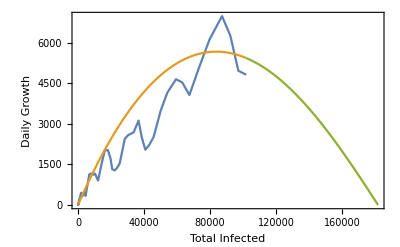
g→-Graphics-

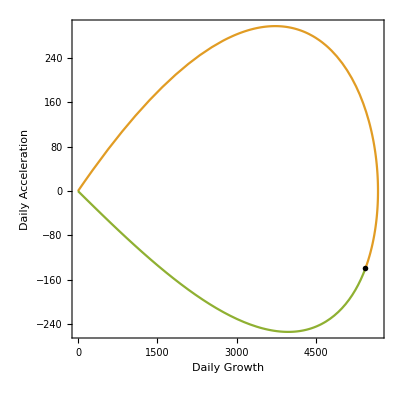
g1→-Graphics-

Denmark

mv 9523

Tmax 13508.

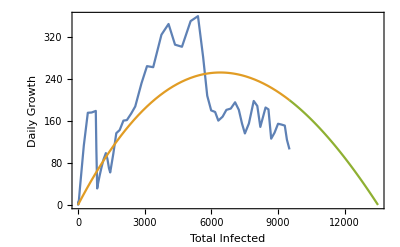
g→-Graphics-

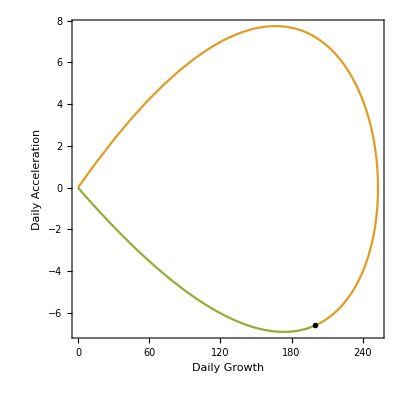
g1→-Graphics-

France

mv 167605

Tmax 197709.

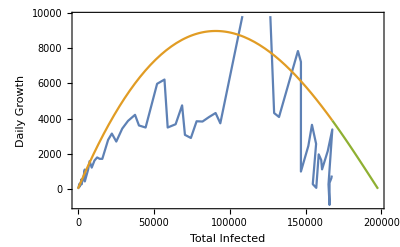
g→-Graphics-

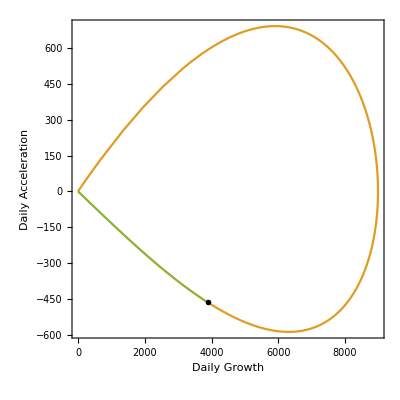
g1→-Graphics-

Germany

mv 165664

Tmax 177620.

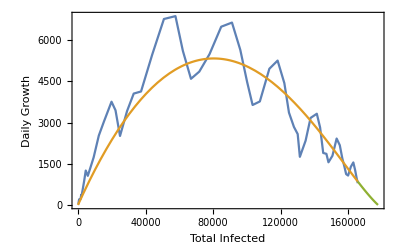
g→-Graphics-

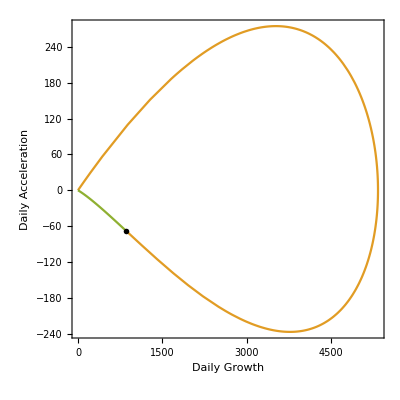
g1→-Graphics-

India

mv 42505

Tmax 104954.

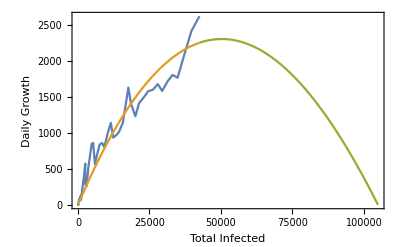
g→-Graphics-

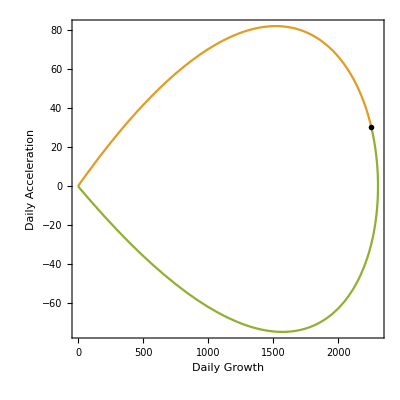
g1→-Graphics-

Israel

mv 16208

Tmax 16208.

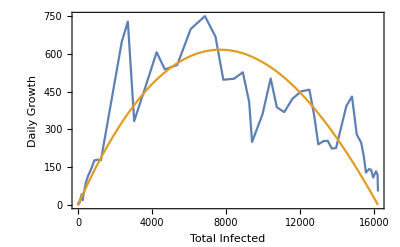
g→-Graphics-

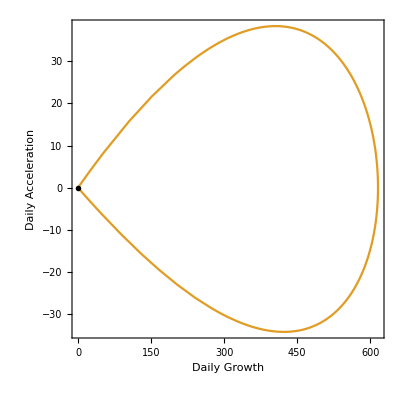
g1→-Graphics-

Italy

mv 210717

Tmax 213169.

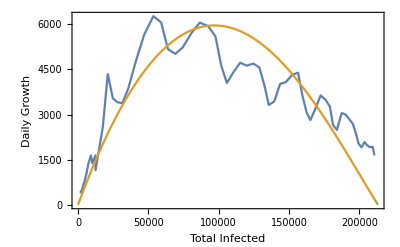
g→-Graphics-

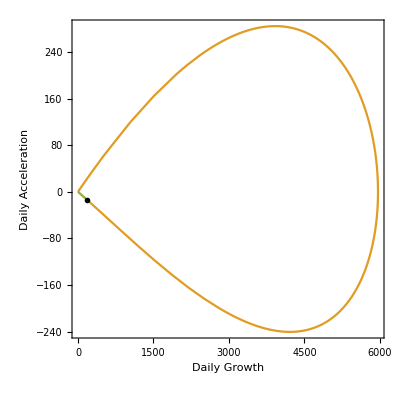
g1→-Graphics-

Japan

mv 14877

Tmax 15805.6

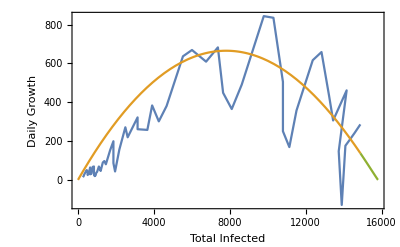
g→-Graphics-

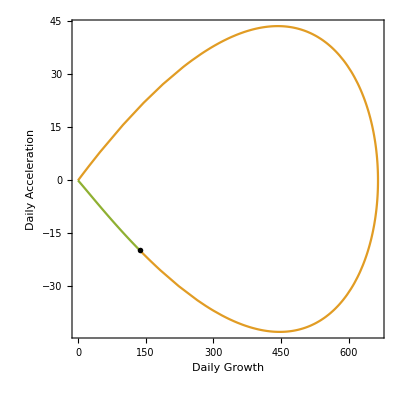
g1→-Graphics-

Poland

mv 13693

Tmax 24151.4

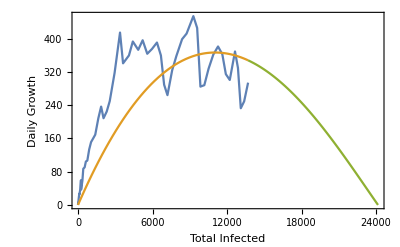
g→-Graphics-

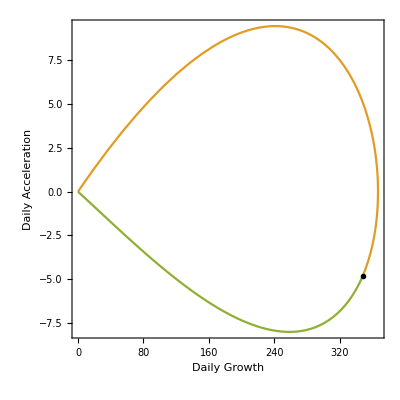
g1→-Graphics-

Russia

mv 134687

Tmax 452019.

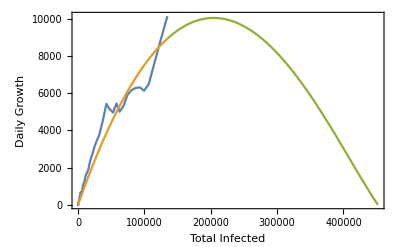
g→-Graphics-

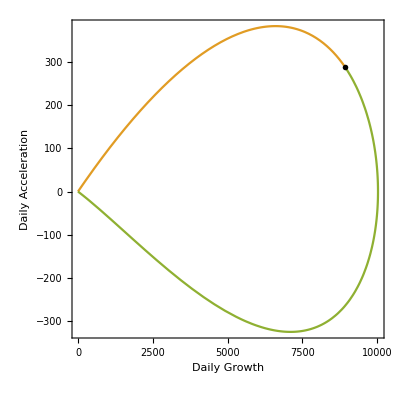
g1→-Graphics-

Singapore

mv 18205

Tmax 24004.3

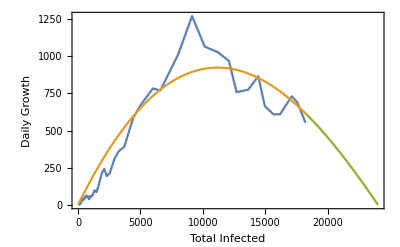
g→-Graphics-

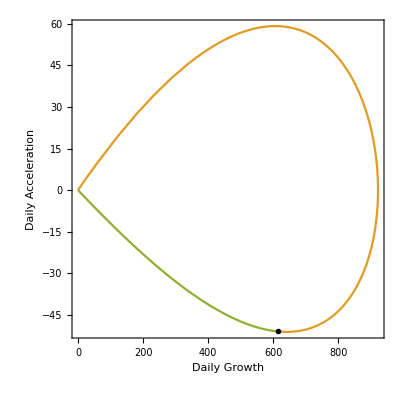
g1→-Graphics-

South Africa

mv 6783

Tmax 34840.1

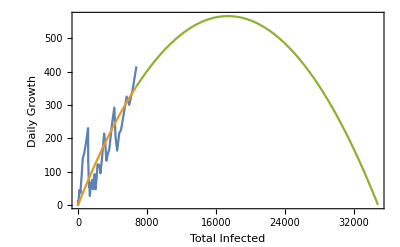
g→-Graphics-

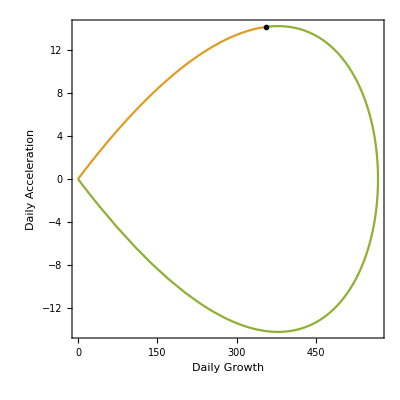
g1→-Graphics-

Spain

mv 217466

Tmax 218769.

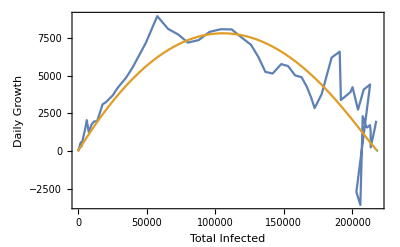
g→-Graphics-

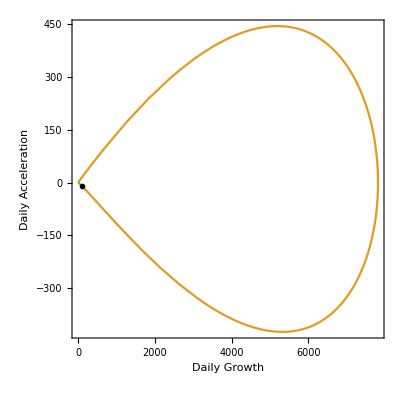
g1→-Graphics-

Sweden

mv 22317

Tmax 34280.3

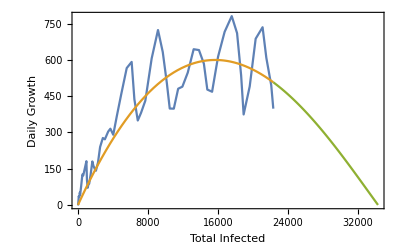
g→-Graphics-

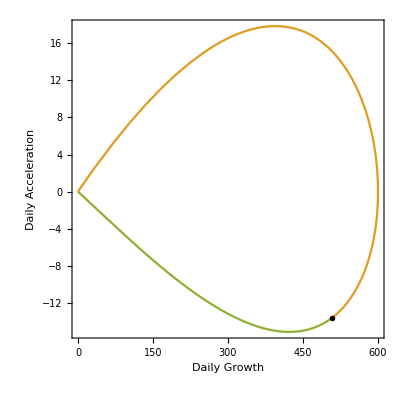
g1→-Graphics-

Turkey

mv 126045

Tmax 140098.

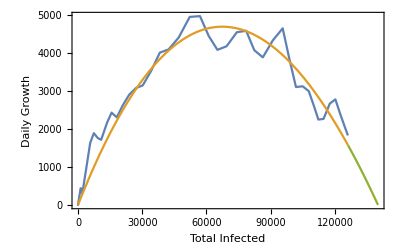
g→-Graphics-

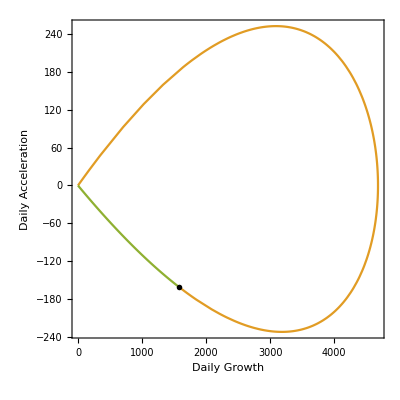
g1→-Graphics-

United Kingdom

mv 186599

Tmax 239028.

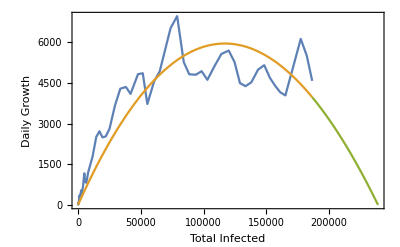
g→-Graphics-

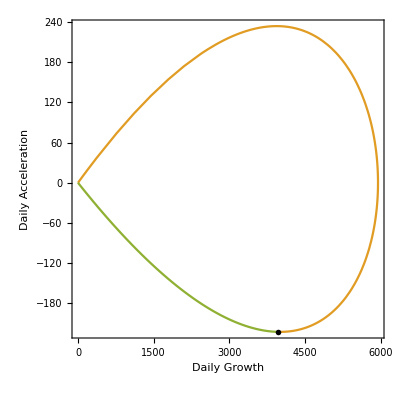
g1→-Graphics-

US

mv 1158040

Tmax 1.45001×10^6

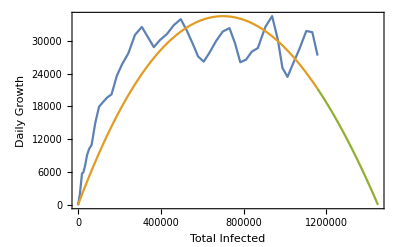
g→-Graphics-

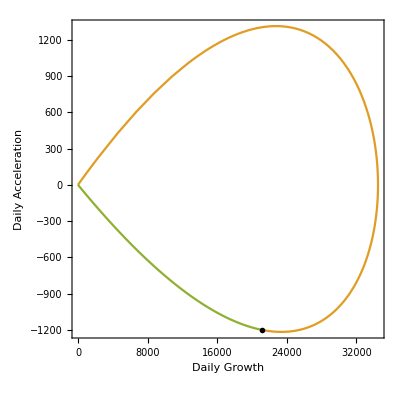
g1→-Graphics-

Dataset[<>]

```mathematica
dd=With[{startDate="1 mar 2020"},worldd[Select[MemberQ[cc,#["Country/Region"]]∧#["Province/State"]==""&],<|"c"->#["Country/Region"],
"flag"->Rasterize[Framed[#data["country"],FrameMargins->0]],
"level"->TimeSeriesWindow[#data,{startDate,Automatic},IncludeWindowTimes->True],"growth"->TimeSeriesWindow[Differences[#data,1,2]/2,{startDate,Automatic},IncludeWindowTimes->True]|>&][All,est2[#,12]&]]
```

```mathematica
Export[$exportDir<>"US_state.gif",dd[Select[#c=="US"&],"g"][[1]]//Normal//Echo]
```

-Graphics-

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/US_state.gif

```mathematica
Export[$exportDir<>"US_swirl.gif",dd[Select[#c=="US"&],"g1"][[1]]//Normal//Echo]
```

-Graphics-

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/US_swirl.gif

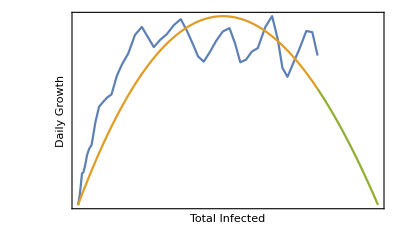
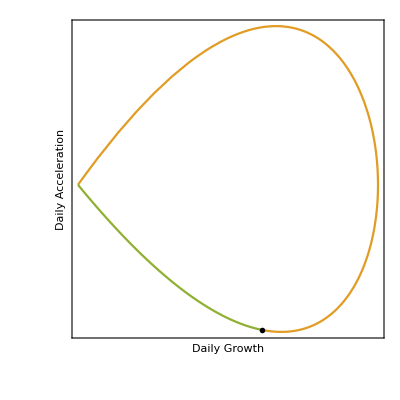
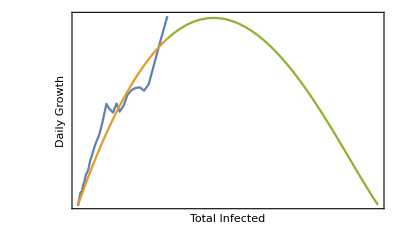
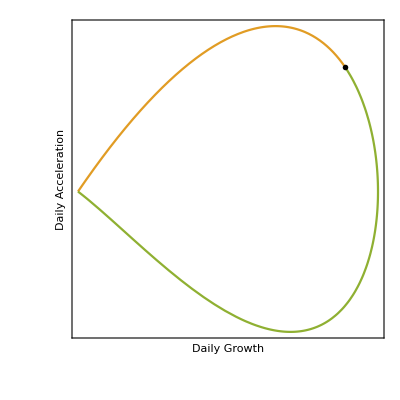
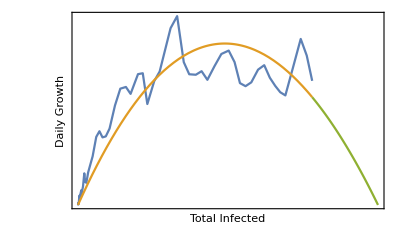
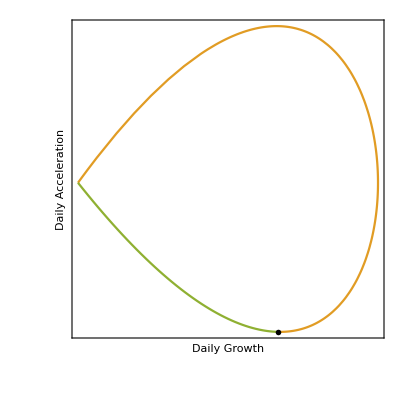
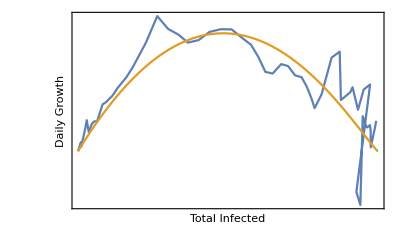
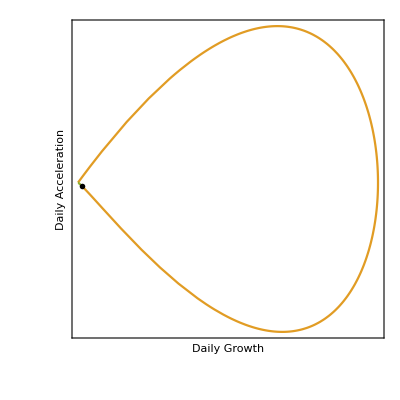
Country | Infected
(estimate) | Infected
(current) | Total Infected/Daily Growth | Daily Growth/Acceleration
-Graphics- | 1450000 | 1158000 | -Graphics- | -Graphics-
-Graphics- | 452000 | 135000 | -Graphics- | -Graphics-
-Graphics- | 239000 | 187000 | -Graphics- | -Graphics-
-Graphics- | 219000 | 218000 | -Graphics- | -Graphics-
-Graphics- | 213000 | 211000 | -Graphics- | -Graphics-
-Graphics- | 198000 | 168000 | -Graphics- | -Graphics-
-Graphics- | 182000 | 102000 | -Graphics- | -Graphics-
-Graphics- | 178000 | 166000 | -Graphics- | -Graphics-
-Graphics- | 140000 | 126000 | -Graphics- | -Graphics-
-Graphics- | 105000 | 43000 | -Graphics- | -Graphics-
-Graphics- | 35000 | 7000 | -Graphics- | -Graphics-
-Graphics- | 34000 | 22000 | -Graphics- | -Graphics-
-Graphics- | 24000 | 14000 | -Graphics- | -Graphics-
-Graphics- | 24000 | 18000 | -Graphics- | -Graphics-
-Graphics- | 16000 | 16000 | -Graphics- | -Graphics-
-Graphics- | 16000 | 15000 | -Graphics- | -Graphics-
-Graphics- | 14000 | 10000 | -Graphics- | -Graphics-

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/table.gif

```mathematica
Export[$exportDir<>"table.gif",Prepend[dd[SortBy[-#total&],{Show[#flag,ImageSize->60],#total, Round[#rho #total,1000],Show[#g,FrameTicks->None],Show[#g1,FrameTicks->None]}&]//Normal,{Style["Country",FontFamily->"Helvetica"],Style["Infected\n(estimate)",FontFamily->"Helvetica"],Style["Infected\n(current)",FontFamily->"Helvetica"],Style["Total Infected/Daily Growth",FontFamily->"Helvetica"],Style["Daily Growth/Acceleration",FontFamily->"Helvetica"]}]//Grid[#,Frame->All,Background->{None,{GrayLevel[.8]}}]&//Echo]
```

```mathematica
Clear[t1,t2,t];
```

```mathematica
t1[τ_]:=γ (S0-t[τ])(R0 t[τ]+Log[1-t[τ]/S0])
```

```mathematica
t2[τ_]:=Evaluate[D[t1[τ],τ]/D[t[τ],τ]//FullSimplify]
```

```mathematica
t[τ]:=τ
```

```mathematica
set={γ->.1,S0->.8,R0->2};
```

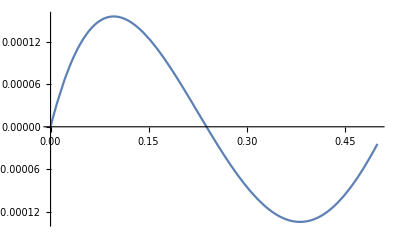

```mathematica
Plot[Evaluate[t1[τ]t2[τ]/.set],{τ,0,.5}]
```

```mathematica
τmax=τ/.FindRoot[Evaluate[t1[τ]/.set]==0,{τ,.5}]
```

0.513585

```mathematica
Clear[t]
```

```mathematica
t[τ_]:=τ
```

```mathematica
offset[c_]:=Module[{x=0,y=0,ppc},If[KeyExistsQ[pp,c],
ppc=pp[c];
If[KeyExistsQ[ppc,"x"],x=ppc["x"]];
If[KeyExistsQ[ppc,"y"],y=ppc["y"]];];
{x,y}];
```

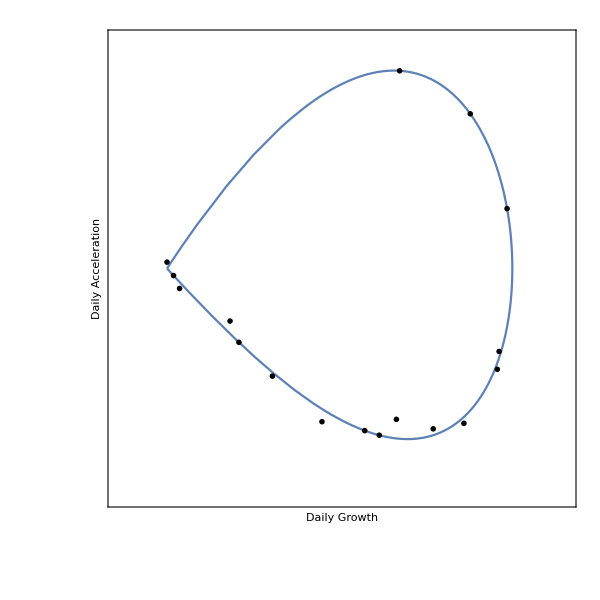

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/countries.gif

```mathematica
Export[$exportDir<>"countries.gif",ParametricPlot[Evaluate[t1[τ]{1,t2[τ]}/.set],{τ,0,τmax},AspectRatio->1,Frame->{{True,False},{True,False}},FrameTicks->None,ImageSize->600,Epilog->(dd[Select[0<#rho≤1&]/*SortBy[#rho&],Inset[#flag,offset[#c]+t1[#rho τmax]{1,t2[#rho τmax]}/.set, Automatic,Scaled[.1]]&]//Normal),PlotRange->{{-.001,.008},{-.00018,.00018}},FrameStyle->White,FrameLabel->(Style[#,16,Black]&/@{"Daily Growth","Daily Acceleration"})]//Echo]
```

```mathematica
cc={"US","Germany","United Kingdom", "Italy", "Spain"}
```

{US,Germany,United Kingdom,Italy,Spain}

```mathematica
pp["Germany"]["x"]=-.0003;
pp["Germany"]["y"]=.00001;
```

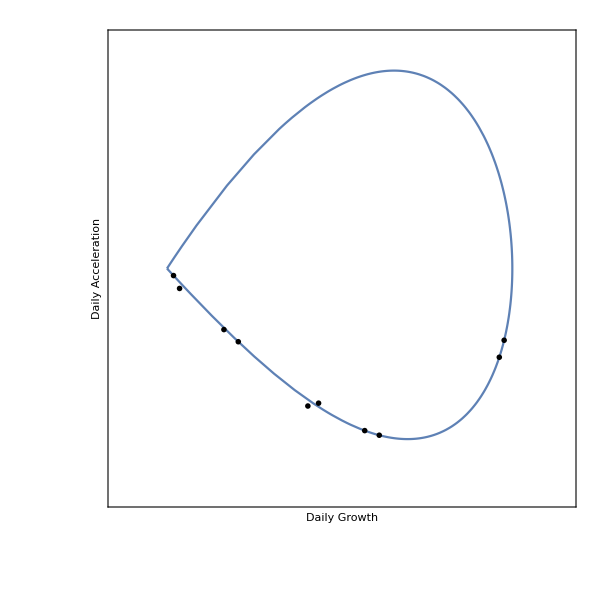

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/cc.gif

```mathematica
Export[$exportDir<>"cc.gif",ParametricPlot[Evaluate[t1[τ]{1,t2[τ]}/.set],{τ,0,τmax},AspectRatio->1,Frame->{{True,False},{True,False}},FrameTicks->None,ImageSize->600,Epilog->(dd[Select[0<#rho≤1∧MemberQ[cc,#c]&]/*SortBy[#rho&],Inset[#flag,offset[#c]+t1[#rho τmax]{1,t2[#rho τmax]}/.set, Automatic,Scaled[.1]]&]//Normal)~Join~(dd[Select[0<#rho2≤1∧MemberQ[cc,#c]&]/*SortBy[#rho2&],Inset[SetAlphaChannel[#flag,.35],offset[#c]+t1[#rho2 τmax]{1,t2[#rho2 τmax]}/.set, Automatic,Scaled[.1]]&]//Normal),
PlotRange->{{-.001,.008},{-.00018,.00018}},FrameStyle->White,FrameLabel->(Style[#,16,Black]&/@{"Daily Growth","Daily Acceleration"})]//Echo]
```

```mathematica
Export[$exportDir<>"infant.gif",dd[All,Labeled[{#rho,QuantityMagnitude[#InfantMortalityFraction]},#flag]&][Show[LogPlot[Evaluate[NonlinearModelFit[First/@#,a Exp[b x],{a,b},x][xx]],{xx,0.15,1},PlotRange->{{.1,1.1},{.0015,.05}},Frame->{{True,False},{True,False}},FrameLabel->(Style[#,14,Black]&/@{"COVID-19 Progress","Infant Mortality Fraction (log)"})],ListLogPlot[#,PlotStyle->None],ImageSize->500]&]//Echo]
```

-Graphics-

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/infant.gif

```mathematica
Export[$exportDir<>"life.gif",dd[All,Labeled[{#rho,QuantityMagnitude[#LifeExpectancy]},#flag]&][Show[Plot[Evaluate[NonlinearModelFit[First/@#,a + b x,{a,b},x][xx]],{xx,0.15,1},PlotRange->{{.1,1.1},All},Frame->{{True,False},{True,False}},FrameLabel->(Style[#,14,Black]&/@{"COVID-19 Progress","Life Expectancy"})],ListPlot[#,PlotStyle->None],ImageSize->500]&]//Echo]
```

-Graphics-

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/life.gif

```mathematica
Export[$exportDir<>"GDP.gif",dd[All,Labeled[{#rho,QuantityMagnitude[#GDPPerCapita]},#flag]&][Show[LogPlot[Evaluate[NonlinearModelFit[First/@#,a Exp[b x],{a,b},x][xx]],{xx,0.15,1},PlotRange->{{.1,1.1},All},Frame->{{True,False},{True,False}},FrameLabel->(Style[#,14,Black]&/@{"COVID-19 Progress","GDP Per Capita (log)"}),Axes->None],ListLogPlot[#,PlotStyle->None,Axes->None],ImageSize->500]&]//Echo]
```

-Graphics-

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/GDP.gif

### Process

```mathematica
Module[{mm,dd},mm=CreateSystemModel[{D[s[t],t]==-β s[t] i[t],D[i[t],t]==β i[t] s[t]-γ i[t],D[r[t],t]==γ i[t]},t, <|"ParameterValues"->{β->.15,γ->.05},"InitialValues"->{i->.01,s->.8,r->0}|>];
dd=SystemModelSimulate[mm,250];
{ss,ii,rr}=Head/@dd[{"s","i","r"},t];]
```

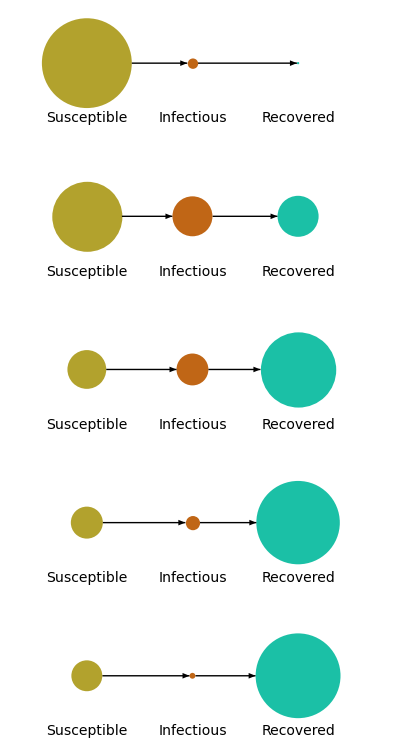

/Users/aleksandartimcenko/notes/u/misc/corona/exhibits/SIR1.gif

```mathematica
Export[$exportDir<>"SIR1.gif",GraphicsGrid[Table[{Graphics[{Text[Style["Susceptible",14],{0,-1.1}],Text[Style["Infectious",14],{2.1,-1.1}],Text[Style["Recovered",14],{4.2,-1.1}],Arrow[{{Sqrt[ss[t]],0},{2.1-Sqrt[ii[t]],0}}],Arrow[{{2.1+Sqrt[ii[t]],0},{4.2-Sqrt[rr[t]],0}}],RGBColor["#B2A22D"],Disk[{0,0},Sqrt[ss[t]]],RGBColor["#C06616"],Disk[{2.1,0},Sqrt[ii[t]]],RGBColor["#1BC0A6"],Disk[{4.2,0},Sqrt[rr[t]]]},PlotRange->{{-1,5.5},{-1.3,1}}]},{t,1,230,50}],ImageSize->400]//Echo]
```

### Turn Ṫ, T̈ into time series...

```mathematica
(*
τ0[T_]:=Total[1/#[[2]]&/@Select[qq,#[[1]]≤T&]];
fq[q_]:=Which[q<1, qv[[1]],q>Length[qv],qv[[-1]],True,Interpolation[Log[qv]][q]];
NMinimize[Evaluate[Log[First/@qq]-fq[α+β τ0[#]]&/@(First/@qq)//Norm],{α,β},,MaxIterations->10000]
*)
```